```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data1=ToExpression/@StringSplit[#," "]&/@Import["debug_data1.txt","Lines"];
data2=ToExpression/@StringSplit[#," "]&/@Import["debug_data2.txt","Lines"];
maxtime=Max[Max[data1⟦All,1⟧],Max[data2⟦All,1⟧]];
datafr=N[{(#⟦2,1⟧+#⟦1,1⟧)/2,Abs[#⟦2,2⟧-#⟦1,2⟧]}&/@Partition[data1,2],10];
```

```mathematica
maxfilter=Compile[{{l,_Real,2},{r,_Integer}},
{Mean[#⟦All,1⟧],Max[#⟦All,2⟧]}&/@Partition[l,2r+1]
];
meanfilter=Compile[{{l,_Real,2},{r,_Integer}},
{Mean[#⟦All,1⟧],Mean[#⟦All,2⟧]}&/@Partition[l,2r+1]
];
```

```mathematica
fin1=Interpolation[DeleteDuplicates[data1,First[#1]==First[#2]&]];
fin2=Interpolation[DeleteDuplicates[data2,First[#1]==First[#2]&]];
```

```mathematica
Plot[{
fin1[x]
},{x,0,maxtime}]
Plot[{
fin2[x]
},{x,0,maxtime}]
```

```mathematica
ListLogPlot[{data1}]
ListLogPlot[{data2}]
```

```mathematica
getdictdata1=data1;
getdictdata2=data2;
```

```mathematica
t1dictdata1=data1;
t1dictdata2=data2;
```

```mathematica
t2dictdata1=data1;
t2dictdata2=data2;
```

```mathematica
getdadata1=data1;
getdadata2=data2;
```

```mathematica
t1dadata1=data1;
t1dadata2=data2;
```

```mathematica
t2dadata1=data1;
t2dadata2=data2;
```

```mathematica
ListLogPlot[{
meanfilter[t2dictdata2,1],
meanfilter[t2dadata2,1]
}]
```

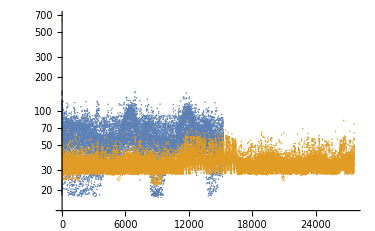
```mathematica
(*
Get,
dict_array,
dict,
*)
-Graphics-
```

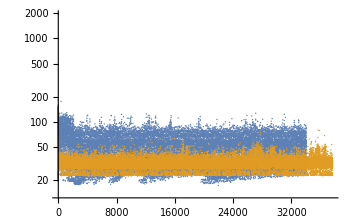
```mathematica
(*
Walk left,
dict_array,
dict,
*)
-Graphics-
```

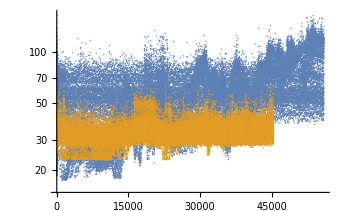
```mathematica
(*
Walk around,
dict_array,
dict,
*)
-Graphics-
```

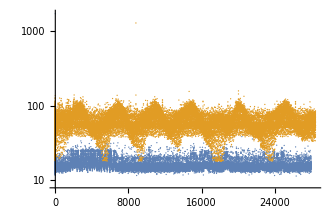
```mathematica
(*
Get,
Blue: array,
Orange:dict,
Array_grid is *much* faster for gets
*)
-Graphics-
```

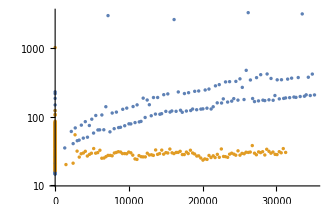
```mathematica
(*
Walk left set test,
Blue: array,
Orange:dict,
Array_grid is *much* slower when setting outside its boundaries
(which forces the boundary to expand)
*)
-Graphics-
```

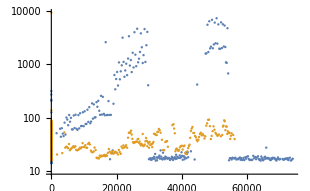
```mathematica
(*
Walk around set test,
Blue: array,
Orange: dict,
Array_grid is truly O(1) for -- and faster than Dict_grid for -- sets within its boundary
*)
-Graphics-
```